# Calculating the uncertainty dimension

In this notebook, we want to determine a relationship between the uncertainty dimension α and the parameters b and ε. We use the uncertainty algorithm described in  Rev. Mod. Phys., vol. 81, no. 333, 2009. We use the same initial conditions used in calculating the escape time scattering function (see EscapeTimeScatteringFunction.nb), but only for shooting angles ϕ_sh∈[1,2]. We choose 20 values of ϵ in the interval (10^-9,10^-5), with h=0.01. We shoot trajectories until the number of uncertain trajectories is 1000.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Equations of motion and orbital parameters

Our initial condition is the point (ρ,θ)=(3,π/2) and we assume that the particle is initially in a circular orbit. This restricts the value of l

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
```

This also restricts the value of U_eff.

```mathematica
Ueff[b_]:=(1-1/3)(1+(l[b]-9b )^2/9);
```

The equations of motion are

```mathematica
ddrho[b_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[b]b-1)/(2 ρ[σ]^2)+(l[b]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[b_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[b]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b^2 Sin[θ[σ]]Cos[θ[σ]]
```

To obtain the initial conditions (ρ'[0],θ'[0]) we use the function below. The angle ϕ_sh is taken with respect to the positive z axis, where clockwise correspond to positive ϕ_sh.

```mathematica
getVelocities[b_,en_,ϕsh_]:=Module[{dρ0,dθ0,result},
dρ0=(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Sin[ϕsh];
dθ0=-(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Cos[ϕsh];
result={dρ0,dθ0}
];
```

## The uncertainty dimension function

We need a function that takes as its input ϕ_sh and outputs the escape time T_e:

```mathematica
TEscape[b_,en_,ϕsh_]:=Module[{initVelocities,escTime},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},MaxSteps->∞];
Return[escTime]
];
```

We also need a function that determines if a particular initial condition is uncertain or not with respect to ϵ

```mathematica
IsUncertain[b_,en_,ϕsh_,epsilon_]:=Module[{result,T0,T1},
T0=TEscape[b,en,ϕsh];
T1=TEscape[b,en,ϕsh+epsilon];
If[Abs[T0-T1]>0.005,result=True,result=False]
];
```

We use 20 values of ϵ to calculate the uncertainty dimension.

```mathematica
epsRange=Subdivide[10^-9,10^-5,19];
```

We also construct a function that obtains the slope of a linear fit to a given set of data points

```mathematica
bestFitSlope[data_]:=Module[{lm,x},lm=LinearModelFit[data,{1,x},x];
First@Pick[lm["BestFitParameters"],lm["BasisFunctions"],x]];
```

Now we construct the function that calculates the uncertainty dimension given parameters b and ε:

```mathematica
getUncDimension[b_,en_]:=Module[{data,numUnc,ϕ,slope},
data=ConstantArray[0,Length[epsRange]]; (*Container of (Log(ϵ), Log(f(ϵ))) data points*)
Table[
numUnc=0; (*Number of uncertain initial conditions*)
SetSharedVariable[numUnc];
(*I want to turn this into a "ParallelWhile" Loop, i.e. I want it to loop until numUnc=1000. I don't know how to yet.*)
ParallelDo[
ϕ=RandomReal[{1,2},WorkingPrecision->10]; (*Initial conditions ϕ∈[1,2]*)
If[IsUncertain[b,en,ϕ,ϵ],numUnc++];
,
{numTraj}
,
Method-> "FinestGrained"
];
data⟦First@Flatten@Position[epsRange,ϵ]⟧={Log[ϵ],Log[numUnc/numTraj]};
,
{ϵ,epsRange}
];
slope=bestFitSlope[data]; (*Get the slope*)
Return[1-slope]
];
```

## Other parameters

We want to see how the uncertainty dimension changes with b∈[0,1] or with ε∈[1.2,3] (for the positive l case). To get the uncertainty dimension, we shoot N= numTraj random trajectories.

```mathematica
MaximumT=10^6;LaunchKernels[6];bRange=Drop[Subdivide[0,1,50],1];εRange=Subdivide[1.2,3,49];numTraj=5000;
```

## Positive l (Constant ε)

```mathematica
$IsPositive=True;
```

```mathematica
uncDim1=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦1;;25⟧}],i//N];//AbsoluteTiming
Export["uncDimData1.mx",Transpose[{bRange⟦1;;25⟧,uncDim1}]]
```

{115371.,Null}

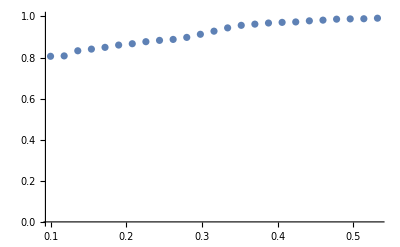

```mathematica
ListPlot[Transpose[{bRange⟦1;;25⟧,uncDim1}],PlotRange->{All,{0,1}}]
```

Weird. I would expect that the uncertainty dimension is smaller as b gets larger. Examine b=0.5 more closely.

```mathematica
uncDim2=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦26;;30⟧}],i//N];//AbsoluteTiming
Export["uncDimData2.mx",Transpose[{bRange⟦26;;30⟧,uncDim2}]]
```

```mathematica
uncDim3=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦31;;35⟧}],i//N];//AbsoluteTiming
Export["uncDimData3.mx",Transpose[{bRange⟦30;;35⟧,uncDim3}]]
```

```mathematica
uncDim4=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦36;;40⟧}],i//N];//AbsoluteTiming
Export["uncDimData4.mx",Transpose[{bRange⟦36;;40⟧,uncDim4}]]
```

```mathematica
uncDim5=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦41;;45⟧}],i//N];//AbsoluteTiming
Export["uncDimData5.mx",Transpose[{bRange⟦41;;45⟧,uncDim5}]]
```

```mathematica
uncDim6=Monitor[Table[getUncDimension[i,1.2],{i,bRange⟦46;;50⟧}],i//N];//AbsoluteTiming
Export["uncDimData6.mx",Transpose[{bRange⟦46;;50⟧,uncDim6}]]
```